Mohamed M. Hammad

Neural Network and Deep Learning with Mathematica                              < >    Ξ

Edited by Hao Feng

## 9 Advanced Activation Functions

Remark:
This chapter provides a Mathematica implementation of the concepts and ideas presented in Chapter 8, [1], of the book titled Artificial Neural Network and Deep Learning: Fundamentals and Theory. We strongly recommend that you begin with the theoretical chapter to build a solid foundation before exploring the corresponding practical implementation. This chapter also serves as a summary of the article titled Deep Learning Activation Functions: Fixed-Shape, Parametric, Adaptive, Stochastic, Miscellaneous, Non-Standard, Ensemble. For more details about activation functions, please refer to Ref [24].”

The activation functions (AFs) play a very crucial role in Neural Networks (NNs) by learning the abstract features through non-linear transformations. Some common properties of the AFs are as follows: a) it should add the non- linear curvature in the optimization landscape to improve the training convergence of the network; b) it should not increase the computational complexity of the model extensively; c) it should not hamper the gradient flow during training. Several AFs have been explored in recent years for deep learning to achieve the above-mentioned properties. For a more comprehensive background, we refer to [24] and the references cited therein.

In the present work, we categorized the AFs into six distinct groups: sigmoid-based, ReLU-based, ELU-based, miscellaneous, non-standard, and ensemble AFs.

Sigmoid-Based AFs: In order to introduce non-linearity into the NNs, the Logistic Sigmoid, and Tanh AFs have been used in the early days. The firing of biological neurons was the motivation for using the Logistic Sigmoid and Tanh AFs with artificial neurons. The Logistic Sigmoid and Tanh AFs majorly suffer from vanishing gradients. Several improvements have been proposed based on the Logistic Sigmoid AF. The most common Sigmoid- based/related functions are Tanh, HardSigmoid, and HardTanh, Penalized Tanh, Soft-Root-Sign, and Sigmoid- Weighted Linear.

ReLU-Based AFs: The saturated output and increased complexity are the key limitations of the above-mentioned Logistic Sigmoid-based AFs. The ReLU has become the state-of-the-art AF due to its simplicity and improved performance. Various variants of ReLU have been investigated by tackling its drawbacks, such as non-utilization of negative values, limited non-linearity, and unbounded output. The most common ReLU-based/related functions are: Leaky Rectified Linear Unit, Parametric ReLU, Randomized ReLU, Random Translation ReLU, Elastic ReLU, Elastic Parametric ReLU, Linearized Sigmoidal Activation, Rectified Linear Tanh, Shifted ReLU, Displaced ReLU and Multi-bin Trainable Linear Unit.

ELU-Based AFs: The major problem faced by the Logistic Sigmoid-based AFs is with its saturated output for large positive and negative input. Similarly, the major problem with ReLU-based AFs is the under-utilization of negative values leading to a vanishing gradient. In order to cope up with these limitations the ELU-based AFs have been used in the literature. The ELU-based AF utilizes the negative values with the help of the exponential function. Several AFs have been introduced in the literature as ELU variants. The most common ELU-based/related functions are Scaled ELU, Parametric ELU, Rectified Exponential Unit, Parametric Rectified Exponential Unit, and Elastic ELU.

Non-Standard AFs: Non-standard AFs include those that combine multiple standard functions or operate on different principles. The common non-standard AFs are Maxout and Softmax.

Miscellaneous AFs: Such as Swish-based/related AFs (Swish, E-Swish, HardSwish), SoftPlus-based/related AFs (SoftPlus, SoftPlus Linear Unit, Mish), Probabilistic AF (Gaussian Error Linear Unit, and Symmetrical Gaussian Error Linear Unit).

Combining AFs: Most of the Sigmoid, Tanh, ReLU, and ELU-based AFs are designed manually which might not be able to exploit the data complexity. Combining AFs are the recent trends. The most common AF are Mixed, Gated, and Hierarchical AFs, Adaptive Piecewise Linear Units, Mexican ReLU, Look-up Table Unit, and Bi-Modal Derivative Sigmoidal AFs. Unlike traditional AFs such as ReLU, Sigmoid, or ELU, which have fixed functional forms, adaptive AFs learn their parameters from the data, allowing the network to adapt more flexibly to different tasks.

In this chapter, we embark on an in-depth exploration of AFs and custom layers within NNs. The primary goal is to provide a comprehensive understanding of how these functions influence the behavior of NNs. We will achieve this through interactive simulations, detailed comparisons, and practical implementations of custom layers. This chapter is structured into three units, each focusing on a specific aspect of AFs and custom layers.

UNIT 9.1: Interactive Exploration of AF:

In this unit, we explore the behavior of AFs by creating interactive Manipulate visualizations. These visualizations allow us to dynamically change the parameters and observe how they affect the AFs. By adjusting parameters such as slope, threshold, and others, we gain deeper insights into how each AF transforms its input and impacts the overall behavior of a NN. This hands-on approach helps to solidify our understanding of the role of AFs in NNs. Through these interactive simulations, you will develop an intuitive grasp of the mathematical underpinnings and practical implications of various AFs. By experimenting with different parameter settings, you will see firsthand how AFs contribute to the non-linear transformations essential for NN learning.

UNIT 9.2: Custom Layers in NNs:

This unit delves into the construction and utilization of custom layers in NNs. Custom layers are fundamental components that allow for the extension and customization of NN architectures to better suit specific tasks. We will explore several key custom layers, including FunctionLayer, ParametricRampLayer, SoftmaxLayer, NetEncoder, and NetDecoder. Key topics covered in this unit include an overview of custom layers and their role in NN design, a detailed exploration of FunctionLayer and how it allows for the definition of arbitrary functions within a network, understanding ParametricRampLayer and its use for implementing piecewise linear functions, an examination of SoftmaxLayer for transforming raw network outputs into probability distributions, and insights into NetEncoder and NetDecoder for preprocessing input data and postprocessing network outputs, respectively. By the end of this unit, you will have a solid understanding of how to create and integrate custom layers into NNs, enhancing their flexibility and capability to tackle a wide range of problems.

UNIT 9.3: Comparison of Some AFs:

This unit provides a detailed comparison of several commonly used AFs. We will analyze the characteristics and performance implications of ReLU, ELU, SELU, GELU, Swish, HardSwish, Mish, SoftPlus, HardTanh, HardSigmoid, Sigmoid, and Tanh. Each AF will be examined in terms of its mathematical formulation, gradient behavior, and suitability for different types of NN architectures. Through this comprehensive comparison, you will gain a clear understanding of the strengths and weaknesses of various AFs, enabling you to make informed decisions when designing and optimizing NNs.

By the end of this chapter, you will have a robust understanding of how AFs shape the learning dynamics of NNs and how custom layers can be leveraged to build more sophisticated and efficient models.

### Interactive Exploration of Activation Functions

code 9.1

(* The goal of the code is to define the logistic function (logisticFunction) and its derivative (logisticDerivative), and create an interactive visualization using the Manipulate function. This visualization allows users to dynamically adjust the input value via a slider, and observe the behavior of both the logistic function and its derivative over the range of x from -5 to 5. The plot includes legends to differentiate between the functions, and highlights the points on the curves corresponding to the current input value: *)

```mathematica
logisticFunction[x_]:=1/(1+Exp[-x])
logisticDerivative[x_]:=logisticFunction[x](1-logisticFunction[x])

Manipulate[
Plot[
{logisticFunction[x],logisticDerivative[x]},
{x,-5,5},
PlotLegends->Placed[{"Logistic Function","Logistic Derivative"},Below],
AxesLabel->{"x","y"},
PlotRange->{All,{0,1}},
Epilog->{
Red,
PointSize[0.03],
Point[{{inputValue,logisticFunction[inputValue]},{inputValue,logisticDerivative[inputValue]}}]
},
PlotLabel->Style[Row[{"Logistic Function and Derivate at Input Value: ",inputValue}],10,Bold],
GridLines->Automatic,
ImageSize->270
],
{{inputValue,0,"Input Value"},-5,5,Appearance->"Labeled"}]
```

code 9.2

(* The goal of the code is to define the Heaviside step function (`heavisideStepFunction`) and the logistic sigmoid function (`logisticSigmoidFunction`), and create an interactive visualization using the `Manipulate` function. This visualization allows users to dynamically adjust the steepness parameter (`k`) via a slider and observe the behavior of both functions over the range of `x` from -5 to 5. The plot includes legends for differentiation, and highlights specific points at (0,0) and (0,1). The interactive control aims to provide an intuitive understanding of how the logistic sigmoid function changes with different steepness parameters, facilitating a comparison with the Heaviside step function: *)

```mathematica
heavisideStepFunction[x_,threshold_]:=If[x<threshold,0,1]
logisticSigmoidFunction[x_,k_]:=1/(1+Exp[-k*x])

Manipulate[
Plot[
{heavisideStepFunction[x,0],logisticSigmoidFunction[x,k]},
{x,-5,5},
PlotStyle->Thick,
AxesLabel->{"x","y"},
PlotLegends->Placed[{"Heaviside Step Function","Logistic Sigmoid (k="<>ToString[k]<>")"},Below],
PlotRange->{0,1},
PlotLabel->"Step Function vs. Logistic Sigmoid Function",
ImageSize->250,
GridLines->Automatic,
Epilog->
{Red,
PointSize[0.02],
Point[{0,0}],
Point[{0,1}]
}
],
{{k,1,"Steepness Parameter (K)"},0.1,10,0.1}]
```

code 9.3

(* The goal of the code is to define the logistic sigmoid function (`logisticSigmoid`) and create an interactive visualization using the `Manipulate` function. This visualization allows users to dynamically adjust the threshold parameter using a slider and observe the behavior of both the standard Unit Step function and the logistic sigmoid function over the range of `x` from -5 to 5. Additionally, it compares the shifted Unit Step function (with an adjustable threshold) to the logistic sigmoid function. The interactive control provides real- time feedback on the threshold value, offering an intuitive understanding of how the step function’s shift affects its comparison to the sigmoid function: *)

```mathematica
logisticSigmoid[x_]:=1/(1+Exp[-x])

Manipulate[
Column[
{
Row[
{
Plot[
{UnitStep[x],logisticSigmoid[x]},
{x,-5,5},
PlotLegends->Placed[{"Step Function","Logistic Sigmoid"},Below],
AxesLabel->{"x","y"},
PlotRange->{All,{0,1}},
PlotStyle->Thick,
GridLines->Automatic,
ImageSize->250
],
Plot[
{UnitStep[x-threshold],logisticSigmoid[x]},
{x,-5,5},
PlotLegends->Placed[{"Shifted Step Function","Logistic Sigmoid"},Below],
AxesLabel->{"x","y"},
PlotRange->{All,{0,1}},
PlotStyle->Thick,
GridLines->Automatic,
ImageSize->250
]
}
],
Row[{"Threshold: ",threshold}]}
],
{{threshold,0,"Threshold"},-5,5,Appearance->"Labeled"}
]
```

code 9.4

(* The goal of the code is to define the logistic sigmoid and hyperbolic tangent (tanh) functions, along with their derivatives, and create visualizations to compare these functions. It calculates the absolute differences between the sigmoid and tanh functions, as well as their derivatives. The code then plots the sigmoid function, tanh function, and their absolute difference over the range of `x` from -5 to 5, and similarly plots the derivatives of these functions and their absolute difference. These visualizations include legends and axis labels to clearly present the comparisons, providing a comprehensive tool to understand the behavior and differences between the sigmoid and tanh functions and their respective derivatives: *)

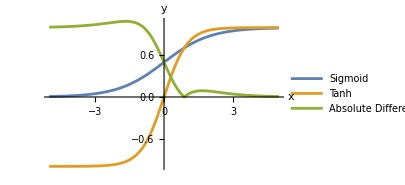

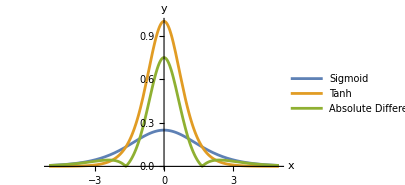

```mathematica
sigmoid[x_]:=1/(1+Exp[-x])
tanh[x_]:=Tanh[x]

absoluteDifference[x_]:=Abs[sigmoid[x]-tanh[x]]

sigmoidDerivative[x_]:=sigmoid[x]*(1-sigmoid[x])
tanhDerivative[x_]:=1-tanh[x]^2

absoluteDifferenceDerivative[x_]:=Abs[sigmoidDerivative[x]-tanhDerivative[x]]

Plot[
{sigmoid[x],tanh[x],absoluteDifference[x]},
{x,-5,5},
PlotLegends->Placed[{"Sigmoid","Tanh","Absolute Difference"},{0.25,0.78}],
AxesLabel->{"x","y"},
PlotRange->All,
ImageSize->300
]

Plot[
{sigmoidDerivative[x],tanhDerivative[x],absoluteDifferenceDerivative[x]},
{x,-5,5},
PlotLegends->Placed[{"Sigmoid","Tanh","Absolute Difference"},{0.25,0.78}],
AxesLabel->{"x","y"},
PlotRange->All,
ImageSize->300
]
```

code 9.5

(* The code defines and explores the behavior of a penalized tanh activation function (penalizedTanh) that adjusts based on a hyperparameter alpha. Using the Manipulate function, it creates an interactive plot that allows users to dynamically adjust alpha with a slider and observe the function’s behavior over the range of x from -3 to 3. This interactive visualization provides an intuitive way to understand how varying alpha impacts the penalized tanh activation function: *)

```mathematica
Manipulate[
Module[
{penalizedTanh,plotRange},
penalizedTanh[x_]:=If[x>0,Tanh[x],alpha*Tanh[x]];
plotRange={-1,1};

Plot[
penalizedTanh[x],
{x,-3,3},
PlotRange->plotRange,
PlotStyle->Thick,
AxesLabel->{"x","f(x)"},
ImageSize->250,
GridLines->Automatic,
PlotLabel->Row[{"Penalized Tanh Activation (α=",alpha,")"}]
]
],
{{alpha,0.5,"α"},0,1,0.1,Appearance->"Labeled"}
]
```

code 9.6

(* The goal of the code is to define and explore the behavior of the Soft-Root- Sign (SRS) activation function and its derivative, parameterized by α and β. Using Mathematica’s `Manipulate` function, it creates an interactive plot that allows users to adjust α and β with sliders, dynamically updating the visualization. The plot displays the SRS function and its derivative over the range of x from -10 to 10, with legends to distinguish between them, and a plot label showing the current parameter values. The plot range is set from-2 to 3 for clear visualization. This interactive tool helps users understand how the SRS function and its derivative change with different α and β values: *)

```mathematica
softRootSign[x_,α_,β_]:=x/((x/α)+Exp[-x/β])
softRootSignDerivative[x_,α_,β_]:=Evaluate[D[softRootSign[t,α,β],t]/.t->x]

Manipulate[
Plot[
{softRootSign[x,α,β],softRootSignDerivative[x,α,β]},
{x,-10,10},
PlotRange->{-2,3},
PlotLabel->StringForm["Soft-Root-Sign for α=`1`, β=`2`",α,β],
PlotLegends->Placed[{"SRS","SRS'"},Below],
ImageSize->250,
GridLines->Automatic
],
{{α,1.6,"α"},1,3,0.1},
{{β,1.5,"β"},0.5,2.5,0.1}
]
```

code 9.7

(* The code defines the ReLU (Rectified Linear Unit) activation function and create an interactive visualization using Mathematica’s Manipulate function. This visualization allows users to dynamically adjust the slope of a line in the subdifferential interval at x=0 using a slider. The plot displays the ReLU function over the range of x from -1 to 1, with a thick blue line for the ReLU function, an adjustable orange line representing possible slopes, and a red point at (0, relu[0]). This interactive tool helps users understand the impact of different slopes in the subdifferential interval at x=0,enhancing comprehension of the ReLU function’s behavior around the origin: *)

```mathematica
relu[x_]:=Max[0,x]

Manipulate[
Plot[
relu[x],
{x,-1,1},PlotStyle->Directive[Blue,Thick],Epilog->{Orange,Line[{{-1/slope,-1},{1/slope,1}}],Red,PointSize[0.02],Point[{0,relu[0]}]
},PlotRange->{-1,1},PlotLabel->Row[{"ReLU function and Possible Slopes at x=0 (Slope =
",NumberForm[slope,{3,2}],")"}],AxesLabel->{"x","f(x)"},ImageSize->310,GridLines->Automatic
],{{slope,0.5,"slope"},0.01,1,0.1}
]
```

code 9.8

(* The code defines two activation functions, ReLU and PReLU, and creates an interactive visualization using Manipulate function to dynamically adjust the parameter α for the PReLU function. The code generates a plot displaying both functions over a specified range, allowing for real-time comparison as the α parameter is adjusted using a slider: *)

```mathematica
ReLUFunction[x_]:=Max[0,x]

PReLUFunction[x_,alpha_]:=Piecewise[{{x,x>=0},{alpha*x,x<0}}]

Manipulate[Plot[{ReLUFunction[x],PReLUFunction[x,alpha]},{x,-3,3},PlotRange->{-3,3},PlotLegends->Placed[{"ReLU","PReLU"},Below],Epilog->Text["α = "<>ToString[alpha],{2,1.5}],PlotLabel->"ReLU and PReLU Activation Functions",ImageSize->250,GridLines->Automatic
],
{{alpha,0.01,"α"},0,1,0.01}
]
```

code 9.9

(* The code defines the ReLU and Parameterized Randomized ReLU (RReLU) activation functions, initializes random parameters for these functions, and creates an interactive visualization using Manipulate function. This visualization allows users to dynamically adjust the parameters α1 and α2 for the RReLU functions using sliders, and observe real-time changes in the plot. The plot displays the ReLU function and two RReLU functions, with shading between the curves to highlight differences. This interactive tool helps users understand the impact of the α parameters on the RReLU functions and compare them to the standard ReLU function: *)

```mathematica
ReLUFunction[x_]:=Max[0,x]

ParameterizedRandomReLU[x_,alpha_]:=Max[alpha x,x]

initialAlpha1=RandomVariate[UniformDistribution[{0,1}]];
initialAlpha2=RandomVariate[UniformDistribution[{0,1}]];

Manipulate[
Plot[{ParameterizedRandomReLU[x,alpha1],ParameterizedRandomReLU[x,alpha2],ReLUFunction[x] },{x,-2,2},PlotRange->{-2,2},Filling->{1->{2}},PlotLegends->Placed[{"First RReLU","Second RReLU","ReLU"},Below],FillingStyle->{LightGray,Opacity[0.3]},GridLines->Automatic,ImageSize->300],{{alpha1,initialAlpha1,"Alpha 1"},0,1,0.01},{{alpha2,initialAlpha2,"Alpha 2"},0,1,0.01}
]
```

code 9.10

(* The code defines the standard ReLU and a Random Transformed ReLU (RTReLU) function, incorporating an interactive interface using Manipulate function. It allows users to dynamically adjust the random seed and the standard deviation σ of a Gaussian distribution, which generates a random offset (a) for the RTReLU function. The plot updates in real-time, displaying both the RTReLU and ReLU functions over a specified range, with dashed lines indicating the offset values (-a and a): *)

```mathematica
RandomTransformedReLU[x_,a_]:=If[x+a>0,x+a,0]

ReLUFunction[x_]:=Max[0,x]

Manipulate[
SeedRandom[randomSeed];

a=RandomVariate[NormalDistribution[0,sigma]];

Plot[{RandomTransformedReLU[x,a],ReLUFunction[x]},{x,-5,5},PlotRange->{Automatic,{-5,5}},PlotLegends->Placed[{"RTReLU","ReLU"},Below],PlotStyle->{Thick,Automatic},GridLines->Automatic,Epilog->{Red,Dashed,Line[{{-a,-5},{-a,5}}],Line[{{a,-5},{a,5}}]},ImageSize->300],{{randomSeed,1,"Random Seed"},1,100,1},
{{sigma,0.5,"σ"},0.1,1,0.1}
]
```

code 9.11

(* The code defines the displaced ReLU, standard ReLU, and ELU (Exponential Linear Unit) activation functions, and creates an interactive interface using Manipulate function. This interface includes a slider that allows users to dynamically adjust the displacement parameter delta (δ) for the displaced ReLU function. The plot, which updates in real-time, displays the displaced ReLU, standard ReLU, and ELU functions over a specified range, enabling users to visually compare them: *)

```mathematica
displacedReLU[x_,delta_]:=If[x>=-delta,x,-delta]

ReLUFunction[x_]:=Max[0,x]

ELUFunction[x_,alpha_]:=If[x>=0,x,alpha*(Exp[x]-1)]

Manipulate[Plot[{displacedReLU[x,delta],ReLUFunction[x],ELUFunction[x,1]},{x,-3,3},PlotLegends->Placed[{"Displaced ReLU","ReLU","ELU"},Below],PlotRange->{{-3,3},{-1.5,3}},GridLines->Automatic,ImageSize->300],{{delta,0.5,"Delta"},0,1,0.1}]
```

code 9.12

(* The code defines the Elastic ReLU (EReLU) function along with its lower and upper bounds, and creates an interactive visualization using Manipulate function. This interface allows users to dynamically adjust the parameter alpha (α) and the random seed, which controls the randomness in the EReLU function. By seeding the random number generator and selecting a random parameter (R) from a uniform distribution, the plot updates in real-time to display the EReLU function and its bounds. The area between the bounds is filled to highlight the function’s variability: *)

```mathematica
lowerBoundFunction[x_,alpha_]:=Piecewise[{{(1-alpha) x,x>0},{"",x<0}}]

upperBoundFunction[x_,alpha_]:=Piecewise[{{(1+alpha) x,x>0},{"",x<0}}]

elasticReLUFunction[x_]:=Piecewise[{{randomParameter x,x>=0},{0,x<0}}]

Manipulate[
SeedRandom[randomSeed];
randomParameter=RandomVariate[UniformDistribution[{1-alpha,1+alpha}]];
Plot[{elasticReLUFunction[x],lowerBoundFunction[x,alpha],upperBoundFunction[x,alpha]},{x,-5,5},PlotLegends->Placed[{"EReLU","(1-α)x","(1+α)x"},Below],Filling->{2->{3}},PlotRange->{-2,5},PlotLabel->"Elastic ReLU Activation Function",ImageSize->300,GridLines->Automatic,PlotStyle->Thick],{{alpha,0.5,"Alpha"},0,1,0.01},{{randomSeed,1,"Seed"},1,100,1}]
```

code 9.13

(* The code defines the Elastic Parametric ReLU (EPReLU) function along with its lower and upper bounds, and creates an interactive visualization using Mathematica’s `Manipulate` function. This interface allows users to dynamically adjust the parameter alpha (α),the negative slope parameter (a), and the random seed, which controls the randomness in the EPReLU function. By seeding the random number generator and selecting a random parameter (R) from a uniform distribution, the plot updates in real-time to display the EPReLU function and its bounds. The area between the bounds is filled to highlight the function’s variability. This interactive tool helps users explore the impact of the parameters alpha (α) and (a) and the effect of randomness on the EPReLU function: *)

```mathematica
lowerBoundEPReLU[x_,alpha_]:=Piecewise[{{(1-alpha) x,x>0},{"",x<0}}]

upperBoundEPReLU[x_,alpha_]:=Piecewise[{{(1+alpha) x,x>0},{"",x<0}}]

elasticPReLUFunction[x_,a_]:=Piecewise[{{randomFactor x,x>=0},{a*x,x<0}}]

Manipulate[
SeedRandom[randomSeed];
randomFactor=RandomVariate[UniformDistribution[{1-alpha,1+alpha}]];
Plot[{elasticPReLUFunction[x,a],lowerBoundEPReLU[x,alpha],upperBoundEPReLU[x,alpha]},{x,-5,5},PlotLegends->Placed[{"EPReLU","(1-α)x","(1+α)x"},Below],Filling->{2->{3}},PlotRange->{-2,5},PlotLabel->"Elastic Parametric ReLU Activation Function",ImageSize->300,GridLines->Automatic,PlotStyle->Thick],
{{alpha,0.5,"Alpha"},0,1,0.01},{{a,0.2,"a"},0,0.9,0.1},{{randomSeed,1,"Seed"},1,100,1}]
```

code 9.14

(* The code defines the Linearized Sigmoidal and Adaptive Linearized Sigmoidal Activation (ALiSA) function along with its upper and lower bounds for both positive and negative input ranges. It creates an interactive interface using Mathematica’s `Manipulate` function, allowing users to dynamically adjust the slope parameters alpha1 (α1) and alpha2 (α2) via sliders. The plot updates in real-time to display the ALiSA function and its bounds, with filled areas highlighting the function’s variability: *)

```mathematica
adaptiveLinearizedSigmoid[x_,alpha1_,alpha2_]:=Piecewise[{{alpha1 x-alpha1+1,1<x<∞},{x,0<=x<=1},{alpha2 x,-∞<x<0}}]

upperBoundPositive[x_,alpha1_]:=Piecewise[{{1.4 alpha1 x-1.4 alpha1+1,1<x<∞},{"",x<1}}]

lowerBoundPositive[x_,alpha1_]:=Piecewise[{{0.7 alpha1 x-0.7 alpha1+1,1<x<∞},{"",x<1}}]

upperBoundNegative[x_,alpha2_]:=Piecewise[{{(1.5 alpha2) x,x<0},{"",x>0}}]

lowerBoundNegative[x_,alpha2_]:=Piecewise[{{(0.7 alpha2) x,x<0},{"",x>0}}]

Manipulate[Plot[{adaptiveLinearizedSigmoid[x,alpha1,alpha2],upperBoundPositive[x,alpha1],lowerBoundPositive[x,alpha1],upperBoundNegative[x,alpha2],lowerBoundNegative[x,alpha2]},{x,-3,3},Filling->{2->{3},4->{5}},PlotRange->{-2,2},PlotLabel->"Adaptive Linearized Sigmoidal Activation Function",ImageSize->300,GridLines->Automatic,PlotStyle->Thick],{{alpha1,0.4,"Alpha1"},0.1,2,0.1},{{alpha2,0.4,"Alpha2"},0,2,0.1}]
```

code 9.15

(* The code defines the Rectified Linear Tanh (ReLTanh) activation function and its derivative, along with the standard Tanh function and its derivative. It creates an interactive interface using Mathematica’s `Manipulate` function, allowing users to dynamically adjust the threshold parameters λplus and λminus via sliders. The plots, which update in real-time, display both the ReLTanh and Tanh functions and their derivatives over a specified range, with filled areas highlighting the differences: *)

```mathematica
reLTanh[x_,λplus_,λminus_]:=Piecewise[{{Tanh'[λplus] (x-λplus)+Tanh[λplus],x>=λplus},{Tanh[x],λminus<x<λplus},{Tanh'[λminus] (x-λminus)+Tanh[λminus],x<=λminus}}]

reLTanhDerivative[x_,λplus_,λminus_]:=Piecewise[{
{Tanh'[λplus],x>=λplus},{Sech[x]^2,λminus<x<λplus},{Tanh'[λminus],x<=λminus}
}
]

Manipulate[Row[{Plot[{reLTanh[x,λplus,λminus],Tanh[x]},{x,-5,5},PlotRange->{-1.5,1.5},Filling->{1->{2}},PlotLabel->"ReLTanh and Tanh Activation Functions",PlotLegends->Placed[{"ReLTanh","Tanh"},{0.75,0.2}],GridLines->Automatic,ImageSize->250],Plot[{reLTanhDerivative[x,λplus,λminus],1-Tanh[x]^2},{x,-5,5},PlotRange->{-1.5,1.5},Filling->{1->{2}},PlotLabel->"The derivative of ReLTanh and Tanh",PlotLegends->Placed[{"ReLTanh'","Tanh'"},{0.75,0.2}],GridLines->Automatic,ImageSize->250]}],{{λplus,1,"λplus (Threshold)"},0,3,0.1},{{λminus,-1,"λminus (Threshold)"},-3,0,0.1}]
```

code 9.16

(* The code defines the Exponential Linear Unit (ELU) activation function and its derivative, and creates an interactive interface using Mathematica’s Manipulate function. This interface allows users to dynamically adjust the α parameter via a slider. The plot, which updates in real-time, displays both the ELU function and its derivative over a specified range. This interactive tool helps users explore the impact of the α parameter on the ELU function: *)

```mathematica
eluFunction[x_,alpha_:1]:=If[x>=0,x,alpha*(Exp[x]-1)]

eluDerivative[x_,alpha_:1]:=If[x>=0,1,eluFunction[x,alpha]+alpha]

Manipulate[
Plot[{eluFunction[x,alpha],eluDerivative[x,alpha]},{x,-3,3},PlotRange->{-4,4},AxesLabel->{"x","y"},PlotLabel->"ELU Function and its Derivative",PlotLegends->Placed[{"ELU","ELU'"},Below],ImageSize->300,GridLines->Automatic],
{{alpha,1,"Alpha"},0.1,4,Appearance->"Labeled"}]
```

code 9.17

(* The code defines the ReLU, ELU (Exponential Linear Unit), PReLU (Parametric ReLU), and sReLU (Shifted ReLU) activation functions along with their derivatives, and creates an interactive interface using Mathematica’s Manipulate function. This interface allows users to dynamically adjust the alpha parameters for the ELU and PReLU functions via sliders. The plot, which updates in real-time, displays the four activation functions over a specified range, enabling users to compare them and observe the impact of the alpha parameters on the ELU and PReLU functions: *)

```mathematica
relu[x_]:=Max[0,x]
reluDerivative[x_]:=If[x>=0,1,0]

elu[x_,alpha_:1]:=If[x>=0,x,alpha*(Exp[x]-1)]
eluDerivative[x_,alpha_:1]:=If[x>=0,1,elu[x,alpha]+alpha]

prelu[x_,alpha_:0.1]:=If[x>=0,x,alpha*x]
preluDerivative[x_,alpha_:0.1]:=If[x>=0,1,alpha]

srelu[x_]:=Max[-1,x]
sreluDerivative[x_]:=If[x>=-1,1,0]

Manipulate[
Plot[{relu[x],elu[x,eluAlpha],prelu[x,preluAlpha],srelu[x]},{x,-3,3},PlotRange->{-5,5},AxesLabel->{"x","y"},PlotLabel->"Comparison of Activation Functions",PlotLegends->Placed[{"ReLU","ELU","PReLU","sReLU"},Below],ImageSize->300,GridLines->Automatic],{{eluAlpha,1,"ELU Alpha"},0.1,5,Appearance->"Labeled"},{{preluAlpha,0.1,"PReLU Alpha"},0.1,5,Appearance->"Labeled"}]
```

code 9.18

(* The code defines the Scaled Exponential Linear Unit (SELU) activation function and its derivative, and creates an interactive interface using Mathematica’s Manipulate function. This interface allows users to dynamically adjust the lambda (λ) and alpha (α) parameters via sliders. The plot, which updates in real-time, displays both the SELU function and its derivative over a specified range: *)

```mathematica
Clear[selu,seluDerivative,lambda,alpha];

selu[x_,lambda_:1.0,alpha_:1.67326]:=lambda*If[x>0,x,alpha*(Exp[x]-1)]

seluDerivative[x_,lambda_:1.0,alpha_:1.67326]:=lambda*If[x>0,1,alpha*Exp[x]]

Manipulate[
Plot[{selu[x,lambda,alpha],seluDerivative[x,lambda,alpha]},{x,-3,3},PlotRange->{-4,4},AxesLabel->{"x","y"},PlotLabel->"SELU Function and its Derivative",PlotLegends->Placed[{"SELU","SELU'"},Below],ImageSize->300,GridLines->Automatic],{{lambda,1.0,"Lambda"},0.1,2,Appearance->"Labeled"},{{alpha,1.67326,"Alpha"},0.1,2,Appearance->"Labeled"}
]
```

code 9.19

(* The code defines the Parametric Exponential Linear Unit (PELU) activation function, its derivative with respect to x, and its partial derivatives with respect to parameters a and b. It creates an interactive interface using Mathematica’s anipulate function, allowing users to dynamically adjust the values of a and b via sliders. The plot, which updates in real-time, displays the PELU function, its derivative, and its partial derivatives over a specified range: *)

```mathematica
pelu[x_,a_:1,b_:1]:=If[x>=0,(a/b) x,a (Exp[x/b]-1)]

peluDerivative[x_,a_:1,b_:1]:=If[x>=0,a/b,(a/b) Exp[x/b]]

peluPartialDerivativeA[x_,a_:1,b_:1]:=If[x>=0,1/b x,Exp[x/b]-1]

peluPartialDerivativeB[x_,a_:1,b_:1]:=If[x>=0,-a/b^2 x,a/b^2 Exp[x/b]]

Manipulate[Plot[{pelu[x,a,b],peluDerivative[x,a,b],peluPartialDerivativeA[x,a,b],peluPartialDerivativeB[x,a,b]},{x,-3,3},PlotRange->{-5,7},AxesLabel->{"x","y"},PlotLabel->"Parametric Exponential Linear Unit (PELU) and Derivatives",PlotLegends->Placed[{"PELU","PELU'","dPELU/da","dPELU/db"},Below],ImageSize->320,GridLines->Automatic],{{a,0.7,"Parameter a"},0.1,2,Appearance->"Labeled"},{{b,0.6,"Parameter b"},0.1,2,Appearance->"Labeled"}]
```

code 9.20

(* The code defines the Parametric Rectified Exponential Unit (PREU) activation function, its derivative with respect to x, and its partial derivatives with respect to parameters α and β. It creates an interactive interface using Mathematica’s Manipulate function, allowing users to dynamically adjust the values of α and β via sliders. The plot, which updates in real-time, displays the PREU function, its derivative, and its partial derivatives over a specified range: *)

```mathematica
PREU[x_,α_,β_]:=Piecewise[{{α*x,x>0},{α*x*Exp[β*x],x<=0}}]

PREUDerivative[x_,α_,β_]:=D[PREU[t,α,β],t]/. t->x

PREUAlphaDerivative[x_,α_,β_]:=D[PREU[x,s,β],s]/. s->α

PREUBetaDerivative[x_,α_,β_]:=D[PREU[x,α,w],w]/. w->β

Manipulate[Plot[{PREU[x,α,β],PREUDerivative[x,α,β],PREUAlphaDerivative[x,α,β],PREUBetaDerivative[x,α,β]},{x,-2,2},PlotRange->All,PlotLegends->Placed[{"PREU","dPREU/dx","dPREU/dα","dPREU/dβ"},Below],PlotLabel->"PREU and Its Derivatives",ImageSize->300,GridLines->Automatic],{{α,2,"α"},0.1,3,0.1},{{β,1,"β"},0.1,3,0.1}]
```

code 9.21

(* The code defines the Elastic Exponential Linear Unit (EELU) activation function, incorporating coefficient sampling during training where k=max[0,min[s,2]], s∼N(1,σ), σ∼U(0,ϵ), and ϵ∈(0,1]. It creates an interactive interface using Mathematica’s Manipulate function, allowing users to dynamically adjust the values of α, β, and the random seed via sliders. The plot, which updates in real-time, displays the EELU function along with its lower and upper bounds over a specified range: *)

```mathematica
EELU[x_,α_,β_,k_]:=Piecewise[{{k*x,x>0},{α*(Exp[β*x]-1),x<=0}}]

sampleCoefficient[σ_]:=Module[{s},s=RandomVariate[NormalDistribution[1,σ]];
Max[0,Min[s,2]]]

Manipulate[Module[{kValue},SeedRandom[seed];
ϵ=RandomReal[];
σ=RandomVariate[UniformDistribution[{0,ϵ}]];
kValue=sampleCoefficient[σ];
lowerBound[x_,σ_]:=Piecewise[{{(kValue-σ) x,x>0},{"",x<0}}];
upperBound[x_,σ_]:=Piecewise[{{(kValue+σ) x,x>0},{"",x<0}}];
Plot[{EELU[x,α,β,kValue],lowerBound[x,σ],upperBound[x,σ]},{x,-5,5},PlotRange->{-2.5,6},Filling->{2->{3}},PlotLegends->Placed[{"EELU","(k-σ)x (Lower bound)","(k+σ)x (Upper
bound)"},Below],PlotLabel->"Elastic Exponential Linear Unit (EELU)",ImageSize->300,GridLines->Automatic]],{{α,1,"α"},0.1,2,0.1},
{{β,1,"β"},0.1,2,0.1},{{seed,1,"seed"},1,100,1}
]
```

code 9.22

(* The code defines the Elastic Exponential Linear Unit (EELU) activation function, its derivatives with respect to x, α, and β, and incorporates coefficient sampling during training where k=max[0,min[s,2]], s~N(1,σ), σ~U(0,ϵ), and ϵ∈(0,1]. It creates an interactive interface using Mathematica’s Manipulate function, allowing users to dynamically adjust the values of α, β, and the random seed via sliders. The plot, which updates in real-time, displays the EELU function, its lower and upper bounds, and its derivatives over a specified range: *)

```mathematica
Clear[x,α,β,k,u,a,b];

EELU[x_,α_,β_,k_]:=Piecewise[{{k*x,x>0},{α*(Exp[β*x]-1),x<=0}}]

EELUDerivativeX[x_,α_,β_,k_]:=D[EELU[u,α,β,k],u]/. u->x
EELUDerivativeAlpha[x_,α_,β_,k_]:=D[EELU[x,a,β,k],a]/. a->α
EELUDerivativeBeta[x_,α_,β_,k_]:=D[EELU[x,α,b,k],b]/. b->β

sampleCoefficient[σ_]:=Module[{s},s=RandomVariate[NormalDistribution[1,σ]];
Max[0,Min[s,2]]]

Manipulate[Module[{kValue},
SeedRandom[seed];

ϵ=RandomReal[];

σ=RandomVariate[UniformDistribution[{0,ϵ}]];

kValue=sampleCoefficient[σ];

lowerBound[x_,σ_]:=Piecewise[{{(kValue-σ) x,x>0},{"",x<0}}];

upperBound[x_,σ_]:=Piecewise[{{(kValue+σ) x,x>0},{"",x<0}}];

Plot[{EELU[x,α,β,kValue],lowerBound[x,σ],upperBound[x,σ],EELUDerivativeX[x,α,β,kValue],EELUDerivativeAlpha[x,α,β,kValue],EELUDerivativeBeta[x,α,β,kValue]},{x,-5,5},PlotRange->{-2.5,6},Filling->{2->{3}},PlotLegends->Placed[{"EELU","(k-σ)x (Lower bound)","(k+σ)x (Upper bound)","dEELU/dx","dEELU/dα","dEELU/dβ"},Below],PlotLabel->"Elastic Exponential Linear Unit (EELU) and Its Derivatives",ImageSize->320,GridLines->Automatic]
],{{α,1,"α"},0.1,2,0.1},{{β,1,"β"},0.1,2,0.1},{{seed,1,"seed"},1,100,1}
]
```

code 9.23

(* The code defines the Swish activation function and its derivative, and creates an interactive interface using Mathematica’s Manipulate function. This interface allows users to dynamically adjust the β parameter via a slider. The plot, which updates in real-time, displays both the Swish function and its derivative over a specified range: *)

```mathematica
Manipulate[Module[{swishFun,swishDerivativeFun},swishFun[x_]:=x*LogisticSigmoid[β*x];
swishDerivativeFun[x_]:=Module[{s},s=LogisticSigmoid[β*x];
s+x*β*s*(1-s)];
Plot[{swishFun[x],swishDerivativeFun[x]},{x,-5,5},PlotLegends->Placed[{"Swish","Swish Derivative"},Below],PlotRange->{-0.5,2},PlotLabel->"Swish and Its Derivatives",ImageSize->300,GridLines->Automatic]],
{{β,1.0,"Beta"},0.1,5.0,0.1,Appearance->"Labeled"}
]
```

code 9.24

(* The code defines the Exponential Swish (ESwish) activation function and its derivative, and creates an interactive interface using Mathematica’s `Manipulate` function. This interface allows users to dynamically adjust the beta (β) parameter via a slider. The plot, which updates in real-time, displays both the ESwish function and its derivative over a specified range: *)

```mathematica
Manipulate[Module[{eswish,eswishDerivative},eswish[x_,β_]:=β*x*LogisticSigmoid[x];
eswishDerivative[x_,β_]:=eswish[x,β]+LogisticSigmoid[x]*(β-eswish[x,β]);
Plot[{eswish[x,β],eswishDerivative[x,β]},{x,-5,5},PlotLegends->Placed[{"ESwish","ESwish Derivative"},Below],PlotLabel->"ESwish and Its Derivatives",PlotRange->{-1,2.5},ImageSize->300,GridLines->Automatic]],{{β,1.0,"Beta"},1,2,0.1,Appearance->"Labeled"}]
```

code 9.25

(* The code defines the Exponential Linear Unit (ELU), Rectified Linear Unit (ReLU), Swish, and Exponential Swish (ESwish) activation functions, and creates an interactive interface using Mathematica’s Manipulate function. This interface allows users to dynamically adjust the α and β parameters via sliders. The plot, which updates in real-time, displays the ELU, ReLU, Swish, and ESwish functions over a specified range: *)

```mathematica
ELU[x_,α_]:=Piecewise[{{x,x>0},{α*(Exp[x]-1),x<=0}}]

ReLU[x_]:=Max[0,x]

swish[x_,β_]:=x*LogisticSigmoid[β*x]

eswish[x_,β_]:=β*x*LogisticSigmoid[x]

Manipulate[Plot[{ELU[x,α],ReLU[x],swish[x,β],eswish[x,β]},{x,-5,5},PlotLegends->Placed[{"ELU (α)","ReLU","Swish (β)","ESwish (β)"},Below],PlotLabel->"ELU, ReLU, Swish and ESwish",PlotRange->{-2,2.5},ImageSize->300,GridLines->Automatic],{{β,1.0,"Beta"},1,2,0.1,Appearance->"Labeled"},{{α,1.0,"Alpha"},0.1,2,0.1,Appearance->"Labeled"}]
```

code 9.26

(* The code defines the Scaled Gaussian Error Linear Unit (SGELU) activation function with an adjustable α parameter, along with the Gaussian Error Linear Unit (GELU), Rectified Linear Unit (ReLU), and Exponential Linear Unit (ELU) activation functions for comparison. It creates an interactive interface using Mathematica’s Manipulate function, allowing users to dynamically adjust the α parameter for the SGELU function via a slider. The plot, which updates in real-time, displays the SGELU, GELU, ReLU, and ELU functions over a specified range: *)

```mathematica
SGELU[x_,alpha_:1.702]:=alpha x Erf[x/Sqrt[2]]

GELU[x_]:=x/2 (1+Erf[x/Sqrt[2]])

ReLU[x_]:=Max[0,x]

ELU[x_,alpha_:1]:=Piecewise[{{alpha (Exp[x]-1),x<0},{x,x>=0}}]

Manipulate[Plot[{SGELU[x,alpha],GELU[x],ReLU[x],ELU[x,1]},{x,-3,3},PlotLegends->Placed[{"SGELU","GELU","ReLU","ELU"},Below],PlotLabel->"SGELU, GELU, ReLU, and ELU",AxesLabel->{"x","y"},PlotRange->{-1,6},ImageSize->300,GridLines->Automatic],
{{alpha,1.702,"Alpha (SGELU)"},0.5,2,Appearance->"Labeled"},TrackedSymbols:>{alpha}
]
```

code 9.27

(* The code defines the Maxout activation function, which takes the maximum of two linear functions f1(x)=w1⋅x+b1 and f2(x)=w2⋅x+b2 defined by parameters w1, b1, w2, and b2: Maxout(x)=max(f1(x),f2(x)). This diagram is 2D and only show how maxout behaves with a 1D input. It creates an interactive interface using Mathematica’s Manipulate function, allowing users to dynamically adjust these parameters via sliders. The plot, which updates in real-time, displays the linear functions and the Maxout function over a specified range, and highlights specific points where the functions are evaluated. This interactive tool helps users explore the impact of the parameters on the Maxout function. By adjusting the sliders, users can see how changing the parameters affects the Maxout function and how it can be used to implement the ReLU, LReLU and PReLU functions, etc: *)

(* The Maxout function approximates the convex function formed by the maximum of f1(x) and f2(x). By adjusting the parameters w1, b1, w2, and b2, you can see how the Maxout unit approximates this convex function through different linear segments. The dashed lines represent the linear functions f1(x) and f2(x), respectively: *)

```mathematica
maxout[x_,w1_,b1_,w2_,b2_]:=Max[w1 x+b1,w2 x+b2]

f1[x_,w1_,b1_]:=w1 x+b1
f2[x_,w2_,b2_]:=w2 x+b2

Manipulate[Plot[{f1[x,w1,b1],f2[x,w2,b2],maxout[x,w1,b1,w2,b2]},{x,-10,10},PlotRange->{-10,10},
PlotStyle->{Dashed,Dashed,Directive[Opacity[0.5],Thick]},PlotLegends->Placed[{"f1","f2","Maxout"},Below],PlotLabel->"Maxout Unit and Linear Functions",Epilog->{PointSize[0.02],Point[{{1,f1[1,w1,b1]},{1,f2[1,w2,b2]}}]},ImageSize->300,GridLines->Automatic
],{{w1,1,"w1"},-2,2},{{b1,0,"b1"},-2,2},{{w2,0,"w2"},-2,2},{{b2,0,"b2"},-2,2}
]
```

code 9.28

(* The code defines the Maxout activation function, which takes the maximum of three linear functions f1(x)=w1⋅x+b1, f2(x)=w2⋅x+b2, and f3(x)=w3⋅x+b3 defined by parameters w1, b1, w2, b2, w3,and b3: Maxout(x)=max(f1(x),f2(x),f3(x)). This diagram is 2D and only show how maxout behaves with a 1D input. The code creates an interactive interface using Mathematica’s Manipulate function, allowing users to dynamically adjust these parameters via sliders. The plot, which updates in real-time, displays the three linear functions and the Maxout function over a specified range, and highlights specific points where the functions are evaluated. *)

(* In this code, you can adjust the parameters w1, b1, w2, b2, w3, and b3 to see how the Maxout unit approximates the convex function formed by the maximum of f1(x), f2(x) and f3(x). The dashed lines represent the linear functions f1(x), f2(x) and f3(x), respectively: *)

```mathematica
maxout[x_,w1_,b1_,w2_,b2_,w3_,b3_]:=Max[w1 x+b1,w2 x+b2,w3 x+b3]

f1[x_,w1_,b1_]:=w1 x+b1
f2[x_,w2_,b2_]:=w2 x+b2
f3[x_,w3_,b3_]:=w3 x+b3

Manipulate[Plot[{f1[x,w1,b1],f2[x,w2,b2],f2[x,w3,b3],maxout[x,w1,b1,w2,b2,w3,b3]},{x,-10,10},PlotRange->{-10,10},PlotStyle->{Dashed,Dashed,Dashed,Directive[Opacity[0.5],Thick]},PlotLegends->Placed[{"f1","f2","f3","Maxout"},Below],PlotLabel->"Maxout Unit and Linear Functions",Epilog->{PointSize[0.02],Point[{{1,f1[1,w1,b1]},{1,f2[1,w2,b2]},{1,f3[1,w3,b3]}}]},ImageSize->300,GridLines->Automatic],{{w1,1,"w1"},-3,3},{{b1,-2,"b1"},-3,3},{{w2,-1,"w2"},-3,3},{{b2,-2,"b2"},-3,3},{{w3,0,"w3"},-3,3},{{b3,0,"b3"},-3,3}]
```

code 9.29

(* The code defines the softmax function, which converts a vector of inputs into a probability distribution. It creates an interactive interface using Mathematica’s Manipulate function, allowing users to adjust the input values x, y, and z via sliders. The interface displays the inputs and their corresponding softmax probabilities in a grid, visualizes the probabilities using a bar chart, and plots the softmax activation function over a specified range: *)

```mathematica
softmax[inputs_]:=Module[{expInputs,expSum},expInputs=Exp[inputs];
expSum=Total[expInputs];
expInputs/expSum]

Manipulate[Module[{inputs,probabilities},inputs={x,y,z};
probabilities=softmax[inputs];
Column[{Grid[{{"Inputs","Softmax Probabilities"},{inputs,probabilities}}],BarChart[probabilities,ChartLabels->Range[3],PlotRange->{0,1},ChartStyle->"Rainbow",AxesLabel->{"Class","Probability"},PlotLabel->"Softmax Probabilities",ImageSize->300],Plot[Evaluate[softmax[{x,y,z}]],{x,-3,3},PlotRange->{{-3,3},{0,1}},PlotStyle->{Purple,Green,Red},PlotLabel->"Softmax Activation Function",ImageSize->300,GridLines->Automatic]}]],{{x,1,"Input x"},-3,3,Appearance->"Labeled"},{{y,0,"Input y"},-3,3,Appearance->"Labeled"},
{{z,-1.0,"Input z"},-3.0,3.0,Appearance->"Labeled"}
]
```

code 9.30

(* The code defines the Leaky Rectified Linear Unit (LReLU) and Exponential Linear Unit (ELU) activation functions, and creates a mixed activation function that combines these two functions using a weighted sum controlled by the parameter Rho (ρ). It also computes the derivative of the mixed activation function. Using Mathematica’s Manipulate function, the code creates an interactive interface allowing users to adjust the parameters ρ, α, and β via sliders. The interface generates example input data, applies the mixed activation function and its derivative to this data, and plots the results: *)

```mathematica
lreluFunction[x_,alpha_]:=If[x>0,x,alpha*x]

eluFunction[x_,beta_]:=If[x>0,x,beta*(Exp[x]-1)]

mixedActivation[x_,Rho_,alpha_,beta_]:=Rho*lreluFunction[x,alpha]+(1-Rho)*eluFunction[x,beta]
derivativeMixedActivation[x_,Rho_,alpha_,beta_]:=D[mixedActivation[t,Rho,alpha,be ta],t]/. t->x

data=Range[-5,5,0.1];
n=Length[data];

Manipulate[Module[{outputData,outputDataderivative},outputData=Table[mixedActivation[data[[i]],Rho,alpha,beta],{i,1,n}];
outputDataderivative=Table[derivativeMixedActivation[data[[i]],Rho,alpha,beta],{i,1,n}];
ListLinePlot[{Transpose[{data,outputData}],Transpose[{data,outputDataderivative}]},PlotRange->{-2,3},PlotLegends->Placed[{"mixedActivation","mixedActivation'"},Below],PlotLabel->"Mixed Activation Strategy (LReLU and ELU)",ImageSize->300,GridLines->Automatic]],{{Rho,0.1,"Rho"},0,1,0.01},{{alpha,0.5,"Alpha LReLU"},0,1,0.01},{{beta,1,"Beta ELU"},0,2,0.01}]
```

code 9.31

(* The code defines the Leaky Rectified Linear Unit (LReLU) and Exponential Linear Unit (ELU) activation functions, and creates a gated activation function that combines these two functions using a gating mechanism controlled by the parameter omega (ω). It also computes the derivative of the gated activation function. Using Mathematica’s Manipulate function, the code creates an interactive interface allowing users to adjust the parameters ω, α, and β via sliders. The interface generates example input data, applies the gated activation function and its derivative to this data, and plots the results: *

```mathematica
lreluFunction[x_,alpha_]:=If[x>0,x,alpha*x]

eluFunction[x_,beta_]:=If[x>0,x,beta*(Exp[x]-1)]

gatedActivation[x_,omega_,alpha_,beta_]:=Module[{gatingMask,lreluResult,eluResult},gatingMask=LogisticSigmoid[omega*x];
lreluResult=lreluFunction[x,alpha];
eluResult=eluFunction[x,beta];
gatingMask*lreluResult+(1-gatingMask)*eluResult];

derivativeGateActivation[x_,omega_,alpha_,beta_]:=D[gatedActivation[t,omega,alpha,beta],t]/. t->x

data=Range[-5,5,0.1];
n=Length[data];

Manipulate[Module[{outputData,outputGatederivative},outputData=Table[gatedActivation[data[[i]],omega,alpha,beta],{i,1,n}];
outputGatederivative=Table[derivativeGateActivation[data[[i]],omega,alpha,beta],{i,1,n}];
ListLinePlot[{Transpose[{data,outputData}],Transpose[{data,outputGatederivative}]},PlotRange->{-2,3},PlotLabel->"Gated Activation Strategy (LReLU and ELU)",PlotLegends->Placed[{"GateActivation","GateActivation'"},Below],ImageSize->300,
GridLines->Automatic
]
],{{omega,0.5,"Omega"},0,1,0.01},{{alpha,0.5,"Alpha LReLU"},0,1,0.01},{{beta,0.5,"beta ELU"},0,2,0.01}
]
```

code 9.32

(* The code defines the Adaptive Piecewise Linear (APL) activation function, which combines the Rectified Linear Unit (ReLU) with additional linear segments defined by parameters a and b. Using Mathematica’s Manipulate function, the code creates an interactive interface allowing users to adjust these parameters via sliders. The interface generates a plot of the APL function over a specified range of input values, which updates in real-time as the parameters are adjusted: *)

```mathematica
APL[x_,a_,b_]:=Module[{S,terms},S=Length[a];
terms=Table[a[[s]]*Max[0,-x+b[[s]]],{s,S}];
Max[0,x]+Total[terms]]

Manipulate[Plot[APL[x,aValues,bValues],{x,-5,5},
PlotRange->All,AxesLabel->{"x","h(x)"},PlotLabel->"Adaptive Piecewise Linear Unit (APL)",ImageSize->300,GridLines->Automatic
],{{aValues,{0,0,0},"a values"},{-1,-1,-1},{3,3,3},Appearance->"Labeled"},{{bValues,{0,0,0},"b values"},{-3,-3,-3},{3,3,3},Appearance->"Labeled"}
]
```

code 9.33

(* The code defines a Mexican hat type function, 𝛷(𝑎,𝜆,𝑥)=max(𝜆−| 𝑥−𝑎|,0), and creates an interactive interface using Mathematica’s Manipulate function. This interface allows users to adjust the parameters a and λ via sliders. The plot, which updates in real-time, displays the Mexican hat type function over a specified range of input values: *)

```mathematica
ϕ[a_,λ_,x_]:=Max[λ-Abs[x-a],0]

Manipulate[Plot[ϕ[a,λ,x],{x,a-2 λ,a+2 λ},PlotRange->{{-9,9},{-0.5,3}},AxesLabel->{"x","ϕ(a,λ)(x)"},PlotLabel->StringForm["Mexican hat type function ϕ(a,λ)(x) \n for a = `1`, λ =
`2`",a,λ],ImageSize->300,GridLines->Automatic],
{{a,0,"a"},-5,5,0.1},{{λ,1,"λ"},0.1,3,0.1}
]
```

code 9.34

(* The code defines a Mexican hat type function, a PReLU function, and a MeLU function that combines PReLU with a linear combination of Mexican hat type functions. This Manipulate allows you to interactively control the coefficients, centers, and widths of the MeLU Function, Mexican Hat Type functions, and PReLU updating the plot in real-time. Adjust the sliders to observe the changes in the MeLU function and its components. This code introduces a Random Seed slider (seed) that allows you to control the seed for the random number generation. Start with initial random values for the coefficients. These coefficients will be adjusted during the training process. The coefficients will be randomly generated (initialized) whenever the seed is changed (In practical applications, the coefficients in models like MeLU are typically learned from data using optimization techniques.): *)

```mathematica
phi[a_,λ_][x_]:=Max[λ-Abs[x-a],0]

MeLU[x_,α_,coefficients_,centers_,widths_]:=PReLU[x,α]+Sum[coefficients[[i]]*phi[centers[[i]],widths[[i]]][x],{i,Length[coefficients]}]

PReLU[x_,α_]:=Max[x,α x]

Manipulate[SeedRandom[seed];
coefficients=RandomReal[{-1,1},9];

widths=Table[width,{i,9}];

centers=Table[i+shift,{i,-4,4,1}];

Plot[{PReLU[x,α],MeLU[x,α,coefficients,centers,widths],Evaluate@Table[phi[centers[[i]],widths[[i]]][x],{i,Length[centers]}]},{x,-6,6},PlotStyle->{Directive[Red,Thick],Thick,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed,Dashed},PlotLegends->{"PReLU","MeLU(x)","Mexican Hat Function 1","Mexican Hat Function 2","Mexican Hat Function 3","Mexican Hat Function 4","Mexican Hat Function 5","Mexican Hat Function 6","Mexican Hat Function 7","Mexican Hat Function 8","Mexican Hat Function 9"},AxesLabel->{"x","y"},PlotRange->All,PlotLabel->"MeLU (PReLU + Linear Combination of 8 Mexican Hat Type Functions)",GridLines->{centers,None},GridLinesStyle->Directive[Red,Dashed],ImageSize->400],{{seed,123,"Random Seed"},1,1000,1,Appearance->"Labeled"},{{shift,0.5,"centers"},0.1,1,0.1,Appearance->"Labeled"},{{width,0.5,"widths"},0.1,1.5,0.1,Appearance->"Labeled"},{{α,0.3,"α"},0.1,1,0.1,Appearance->"Labeled"},TrackedSymbols:>{seed,shift,width,α}
]
```

code 9.35

(* The LuTU activation function is defined using linear interpolation between anchor points based on the specified definition ((1/s) (yi[[i]] (xi[[i+1]]- x)+yi[[i+1]] (x-xi[[i]]))). The function is linearly interpolated between yi and yi+1 for any input value x between xi and xi+1. The function is plotted for three different sets of anchor points: random points, ReLU points, and LReLU points. The plot shows how the LuTU function behaves based on these different anchor points. The points are marked in red, blue, and green, respectively, on the plot: *)

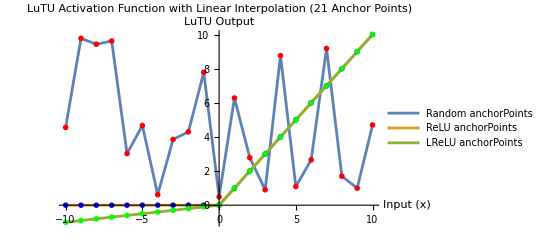

```mathematica
SeedRandom[123];

RandomanchorPoints=Table[{i,RandomReal[{0,10}]},{i,-10,10}];

ReLUanchorPoints=Table[{i,Max[0,i]},{i,-10,10}];

LReLUanchorPoints=Table[{i,Max[0.1 i,i]},{i,-10,10}];

LuTU[x_,anchorPoints_]:=Module[{n,xi,yi,s,i},n=Length[anchorPoints];
xi=anchorPoints[[All,1]];
yi=anchorPoints[[All,2]];
s=xi[[2]]-xi[[1]];
For[i=1,i<n,i++,If[x>=xi[[i]]&&x<=xi[[i+1]],Return[(1/s) (yi[[i]] (xi[[i+1]]-x)+yi[[i+1]] (x-xi[[i]]))]]];
Return[0];
]

Plot[{LuTU[x,RandomanchorPoints],LuTU[x,ReLUanchorPoints],LuTU[x,LReLUanchorPoints]},{x,-10,10},PlotRange->All,AxesLabel->{"Input (x)","LuTU Output"},PlotLabel->"LuTU Activation Function with Linear Interpolation (21 Anchor
Points)",Epilog->{Red,PointSize[0.01],Point[RandomanchorPoints],Blue,Point[ReLUanchorPoints],Green,Point[LReLUanchorPoints]},ImageSize->400,PlotLegends->{"Random anchorPoints","ReLU anchorPoints","LReLU anchorPoints"}]
```

code 9.36

(* The smoothing function is defined as 1/(2 τ) (1+Cos[π/τ x]) for-τ<=x<=τ, and 0 otherwise. The code also defines its derivative with respect to x. Using the Manipulate function, the parameter τ can be adjusted interactively via a slider. The plot, which updates in real-time, shows the smoothing function and its derivative, helping users explore the behavior of these functions with varying values of τ: *)

```mathematica
smoothingFunction[x_,τ_]:=Piecewise[{{1/(2 τ) (1+Cos[π/τ x]),-τ<=x<=τ},{0,True}}
]

derivativeFunction[x_,τ_]:=D[smoothingFunction[t,τ],t]/. t->x

Manipulate[Plot[{smoothingFunction[x,τ],derivativeFunction[x,τ]},{x,-2 τ,2 τ},PlotRange->{{-2,2},{-7,7}},AxesLabel->{"x","y"},PlotLabel->StringForm["Smoothing Function and Its Derivative for τ = ``",τ],PlotLegends->Placed[{"Smoothing Function","Derivative"},Below],ImageSize->300,GridLines->Automatic],{{τ,1,"τ"},0.5,1.5,0.1,Appearance->"Labeled"}]
```

code 9.37

(* The smoothed activation function is defined as the sum of individual terms, each involving a learnable parameter yi and a cosine smoothing mask r(x-xi,t s). This code visualizes the individual cosine smoothing functions, the scaled versions of these functions, and the overall smoothed activation function. The anchor points are marked on the plots to show their locations. By adjusting the parameters and visualizing the results, one can explore the behavior of the smoothed activation function and its components: *)

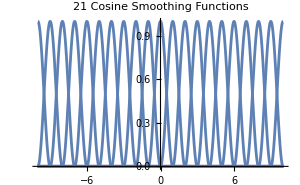

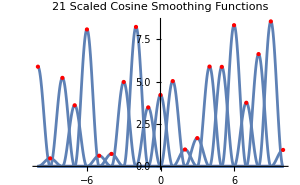

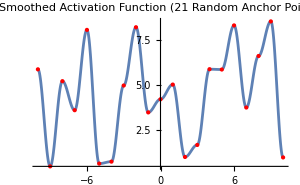

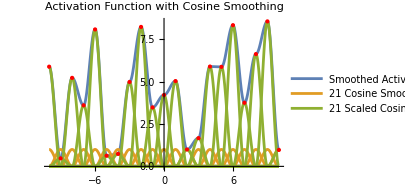

```mathematica
smoothingFunction[x_,τ_]:=If[-τ<=x<=τ,1/(2 τ) (1+Cos[(π/τ) x]),0]

smoothedActivation[x_,anchorPoints_,t_,s_]:=Module[{xi,yi},xi=anchorPoints[[All,1]];
yi=anchorPoints[[All,2]];
Sum[anchorPoints[[i,2]]*smoothingFunction[x-anchorPoints[[i,1]],t s],{i,1,Length[xi]}]]

anchorPoints=Table[{i,RandomReal[{0,10}]},{i,-10,10,1}];

xi=anchorPoints[[All,1]];

Plot[Table[smoothingFunction[x-anchorPoints[[i,1]],1],{i,1,Length[xi]}],{x,-10,10},PlotRange->All,PlotLabel->"21 Cosine Smoothing Functions",ImageSize->300]

Plot[Table[anchorPoints[[i,2]]*smoothingFunction[x-anchorPoints[[i,1]],1],{i,1,Length[xi]}],{x,-10,10},PlotRange->All,PlotLabel->"21 Scaled Cosine Smoothing Functions",Epilog->{Red,PointSize[0.01],Point[anchorPoints]},ImageSize->300]

Plot[smoothedActivation[x,anchorPoints,1,1],{x,-10,10},PlotRange->All,PlotLabel->"Smoothed Activation Function (21 Random Anchor Points)",Epilog->{Red,PointSize[0.01],Point[anchorPoints]},ImageSize->300]

Plot[{smoothedActivation[x,anchorPoints,1,1],
Table[smoothingFunction[x-anchorPoints[[i,1]],1],{i,1,Length[xi]}],Table[anchorPoints[[i,2]]*smoothingFunction[x-anchorPoints[[i,1]],1],{i,1,Length[xi]}]
},{x,-10,10},PlotRange->All,PlotLabel->"Activation Function with Cosine Smoothing",Epilog->{Red,PointSize[0.01],Point[anchorPoints]},ImageSize->300,PlotLegends->{"Smoothed Activation (Random Anchor Points)","21 Cosine Smoothing
Functions","21 Scaled Cosine Smoothing Functions"}
]
```

code 9.38

(* The code defines the Mixture of Gaussians Unit (MoGU) activation function as a sum of Gaussian functions, each parameterized by λ, μ, and σ, and computes its derivative. Using Mathematica’s Manipulate function, the code creates an interactive interface that allows users to adjust these parameters via sliders. The plots, which update in real-time, display the MoGU activation function and its derivative over a specified range of input values: *)

```mathematica
moguActivation[x_,parameters_]:=Total[parameters[[All,1]]/Sqrt[2 π parameters[[All,3]]^2] Exp[-(x-parameters[[All,2]])^2/(2 parameters[[All,3]]^2)]];

moguDerivative[x_,parameters_]:=D[moguActivation[t,parameters],t]/. t->x;

Manipulate[Column[{Plot[moguActivation[x,{{λ1,μ1,σ1},{λ2,μ2,σ2},{λ3,μ3,σ3}}],{x,-5,5},PlotRange->All,AxesLabel->{"x","σ_{MoGU}(x)"},PlotLabel->"MoGU Activation Function",PlotLegends->{"MoGU Activation"},GridLines->Automatic],Plot[moguDerivative[x,{{λ1,μ1,σ1},{λ2,μ2,σ2},{λ3,μ3,σ3}}],{x,-5,5},PlotRange->All,AxesLabel->{"x","σ'_{MoGU}(x)"},PlotLabel->"MoGU Activation Derivative",PlotLegends->{"MoGU Derivative"},GridLines->Automatic]}],{{λ1,1,"λ1"},0.1,2,0.1,Appearance->"Labeled"},{{μ1,0,"μ1"},-5,5,0.1,Appearance->"Labeled"},
{{σ1,1,"σ1"},0.1,2,0.1,Appearance->"Labeled"},{{λ2,0.5,"λ2"},0.1,2,0.1,Appearance->"Labeled"},{{μ2,2,"μ2"},-5,5,0.1,Appearance->"Labeled"},{{σ2,0.5,"σ2"},0.1,2,0.1,Appearance->"Labeled"},{{λ3,0.3,"λ3"},0.1,2,0.1,Appearance->"Labeled"},{{μ3,-3,"μ3"},-5,5,0.1,Appearance->"Labeled"},{{σ3,0.8,"σ3"},0.1,2,0.1,Appearance->"Labeled"}
]
```

code 9.39

(* The code defines the BDAA1 function, which combines two logistic sigmoid functions and depends on the parameter a. It also computes the first derivatives of the BDAA1 function with respect to x and a. Using Mathematica’s Manipulate function, the code creates an interactive interface that allows users to adjust the parameter a via a slider. The plot, which updates in real-time, displays the BDAA1 function and its derivatives over a specified range of input values: *)

```mathematica
σLogistic[x_]:=1/(1+Exp[-x])

σBDAA1[x_,a_]:=1/2 (σLogistic[x]+σLogistic[x+a])

σBDAA1DerivativeX[x_,a_]:=D[σBDAA1[x,a],x]

σBDAA1DerivativeA[x_,a_]:=D[σBDAA1[x,t],t]/. t->a

Manipulate[Plot[Evaluate[{σBDAA1[x,a],σBDAA1DerivativeX[x,a],σBDAA1DerivativeA[x,a]}],{x,-15,15},PlotRange->All,PlotLegends->Placed[{"σBDAA1(x)","Derivative with x","Derivative with
a"},Below],PlotLabel->Row[{"a = ",a}],AxesLabel->{"x","σBDAA1(x)"},
ImageSize->300,GridLines->Automatic
],{{a,0,"a"},-10,10,0.1,Appearance->"Labeled"}
]
```

code 9.40

(* The code defines the BDAA2 function, which combines two logistic sigmoid functions with an adjustment factor and depends on the parameter a. It also computes the first derivatives of the BDAA2 function with respect to x and a, as well as the first derivatives of the logistic sigmoid function with respect to x and a. Using Mathematica’s Manipulate function, the code creates an interactive interface that allows users to adjust the parameter a via a slider. The plot displays the BDAA2 function and its derivatives over a specified range of input values: *)

```mathematica
σLogistic[x_]:=1/(1+Exp[-x])

σBDAA2[x_,a_]:=1/2 (σLogistic[x]+σLogistic[x+a]-1)

σLogisticDerivativeX[x_]:=σLogistic[x] (1-σLogistic[x])

σBDAA2DerivativeX[x_,a_]:=1/2 (σLogisticDerivativeX[x]+σLogisticDerivativeX[x+a])

σLogisticDerivativeA[x_,a_]:=σLogistic[x+a] (1-σLogistic[x+a])

σBDAA2DerivativeA[x_,a_]:=1/2 σLogisticDerivativeA[x,a]

Manipulate[
Plot[
{σBDAA2[x,a],σBDAA2DerivativeX[x,a],σBDAA2DerivativeA[x,a]},{x,-15,15},PlotRange->All,PlotLegends->Placed[{"σBDAA2(x)","Derivative with x","Derivative with
a"},Below],PlotLabel->Row[{"a = ",a}],AxesLabel->{"x","σBDAA2(x)"},ImageSize->300,GridLines->Automatic
],{{a,5,"a"},-10,10,0.1,Appearance->"Labeled"}
]
```

code 9.41

(* This code includes the function σBDAA3(x),its first derivative with respect to x, and its first derivative with respect to a in the same plot. The slider allows you to interactively change the value of a, and the plot updates in real-time.*)

```mathematica
σLogistic[x_]:=1/(1+Exp[-x])

σBDAA3[x_,a_]:=1/2 (σLogistic[x+a]+σLogistic[x-a])

σLogisticDerivativeX[x_]:=σLogistic[x] (1-σLogistic[x])

σBDAA3DerivativeX[x_,a_]:=1/2 (σLogisticDerivativeX[x+a]+σLogisticDerivativeX[x-a])

σLogisticDerivativeA[x_,a_]:=σLogistic[x+a] (1-σLogistic[x+a])-σLogistic[x-a] (1-σLogistic[x-a])

σBDAA3DerivativeA[x_,a_]:=1/2 σLogisticDerivativeA[x,a]
Manipulate[Plot[{σBDAA3[x,a],σBDAA3DerivativeX[x,a],σBDAA3DerivativeA[x,a]},{x,-15,15},PlotRange->All,PlotLegends->Placed[{"σBDAA3(x)","Derivative with x","Derivative with
a"},Below],PlotLabel->Row[{"a = ",a}],AxesLabel->{"x","σBDAA3(x)"},ImageSize->300,GridLines->Automatic],{{a,5,"a"},-10,10,0.1,Appearance->"Labeled"}]
```

code 9.42

(* This code includes the function σBDAA4(x),its first derivative with respect to x, and its first derivative with respect to a in the same plot. The slider allows you to interactively change the value of a, and the plot updates in real-time.*)

```mathematica
σLogistic[x_]:=1/(1+Exp[-x])

σBDAA3[x_,a_]:=1/2 (σLogistic[x+a]+σLogistic[x-a])

σBDAA4[x_,a_]:=σBDAA3[x,a]-1/2

σLogisticDerivativeX[x_]:=σLogistic[x] (1-σLogistic[x])
σBDAA3DerivativeX[x_,a_]:=1/2 (σLogisticDerivativeX[x+a]+σLogisticDerivativeX[x-a])

σBDAA4DerivativeX[x_,a_]:=σBDAA3DerivativeX[x,a]

σLogisticDerivativeA[x_,a_]:=σLogistic[x+a] (1-σLogistic[x+a])-σLogistic[x-a] (1-σLogistic[x-a])

σBDAA3DerivativeA[x_,a_]:=1/2 σLogisticDerivativeA[x,a]

σBDAA4DerivativeA[x_,a_]:=σBDAA3DerivativeA[x,a]

Manipulate[Plot[{σBDAA4[x,a],σBDAA4DerivativeX[x,a],σBDAA4DerivativeA[x,a]},{x,-15,15},PlotRange->All,PlotLegends->Placed[{"σBDAA4(x)","Derivative with x","Derivative with
a"},Below],PlotLabel->Row[{"a = ",a}],AxesLabel->{"x","σBDAA(x)"},ImageSize->300,GridLines->Automatic],{{a,-7.5,"a"},-10,10,0.1,Appearance->"Labeled"}]
```

### Custom Layers in Neural Networks

In the ever-evolving field of deep learning, the Wolfram Language provides a comprehensive suite of tools for constructing, training, and deploying neural networks. Mathematica, with its powerful symbolic and numerical capabilities, offers a rich set of built-in functions that simplify the creation of complex neural network architectures. This unit delves into some of these fundamental components, including FunctionLayer, ParametricRampLayer, SoftmaxLayer, NetEncoder, and NetDecoder.

#### FunctionLayer

ElementwiseLayer is designed for situations where you need to apply a function to each element of an input tensor independently. This layer is highly useful for implementing common activation functions (such as ReLU, sigmoid, and tanh) as well as custom transformations. By applying functions element-wise, you can tailor the behavior of your neural network to fit your specific needs, enhancing its performance and interpretability. On the other hand, FunctionLayer takes customization a step further by allowing you to define layers based on arbitrary functions that can operate on entire tensors. This is particularly useful when your desired transformation involves complex operations, multiple inputs, or non-standard tensor manipulations that go beyond element-wise operations.

FunctionLayer[f] represents a net layer that applies function f to its input.

Remarks:

• FunctionLayer is used to define neural nets from usual Wolfram Language code.

• FunctionLayer[f][x] behaves in the same way as f[x].

• The function f should involve only valid operations on arrays that produce an array or an association of arrays.

• Valid operations include arithmetic functions (Plus, Times, etc.), elementary functions (Exp, Sqrt, Sin, etc.), numerical functions (Min, Round, Ramp, etc.), array constructions (Table, ConstantArray, etc.), array operations (Dot, Det, Tr, etc.), descriptive statistics (Mean, StandardDeviation, etc.) and distance and similarities (EuclideanDistance, HammingDistance, etc.). It is also possible to use looping constructs (Map, NestList, FoldList, etc.) and list manipulation functions (Part, Reverse, etc.).

• Function f must take only one argument as input. The argument can be an array or an association of arrays.

• If the argument of f is a unique array, f can be defined by a pure function, a symbol or a composition of these. The resulting layer will have a unique input port called “Input”.

• FunctionLayer can also be given a multiple-argument function f using the syntax FunctionLayer[Apply[f]]. In this case, ports are named automatically.

• FunctionLayer[f,”port”->shape] can be used as in NetGraph to specify the shape, encoder or decoder of a given port.

code 9.43

(* The code demonstrates the creation and usage of a `FunctionLayer` in Mathematica that calculates the standard deviation of a given set of numbers. It shows how to define this `FunctionLayer`, calculate the standard deviation both directly and through the `FunctionLayer`, and extract the underlying function and neural network structure from the `FunctionLayer`. Additionally, it includes a command to display the network graph of the `FunctionLayer`, providing a visual representation of the layer’s architecture. This code is useful for understanding how to encapsulate mathematical functions within neural network layers and interact with these layers programmatically: *)

```mathematica
stdLayer=FunctionLayer[StandardDeviation]

standardDeviationResult=StandardDeviation[{1.3,2.1,2,3.56,2.4,4.31,6.35,7.,8.2}]

stdLayerResult=stdLayer[{1.3,2.1,2,3.56,2.4,4.31,6.35,7.,8.2}]

extractedFunction=NetExtract[stdLayer,"Function"]

extractedNet=NetExtract[stdLayer,"Net"]

networkGraph=NetGraph[stdLayer]
```

FunctionLayer[…]

2.49366

2.49366

StandardDeviation

AggregationLayer[…]

NetGraph[…]

code 9.44

(* The code defines and utilizes a custom function that computes various statistical measures (Mean, Variance, Standard Deviation, Median, Min, and Max) for a given matrix of numerical values. It demonstrates the creation of a `FunctionLayer` from this custom function and its conversion into a `NetGraph` to facilitate its application within a neural network framework. The code generates a sample input matrix, applies both the custom function and the `FunctionLayer` to this matrix, and computes the same statistical measures directly using Mathematica’s built-in functions. Finally, it compares the results from these three methods to ensure consistency and accuracy in the computation of the statistical measures: *)

```mathematica
statisticalMeasuresFunction=Function[<|"Mean"->Mean[#],"Variance"->Variance[#],"StandardDeviation"->StandardDeviation[#],"Median"->Median[#],"Min"->Min[#],"Max"->Max[#]|>];

statisticalMeasuresLayer=NetGraph@FunctionLayer[statisticalMeasuresFunction]

inputMatrix=N@Array[Sqrt[#1+2*#2]&,{7,3}]

statisticalMeasuresFunctionResult=statisticalMeasuresFunction[inputMatrix];

statisticalMeasuresLayerResult=statisticalMeasuresLayer[inputMatrix];

meanResult=Mean[inputMatrix];
varianceResult=Variance[inputMatrix];
standardDeviationResult=StandardDeviation[inputMatrix];
medianResult=Median[inputMatrix];
minResult=Min[inputMatrix];
maxResult=Max[inputMatrix];

comparisonResults=<|"Function"->statisticalMeasuresFunctionResult,"FunctionLayer"->statisticalMeasuresLayerResult,"Direct"-><|"Mean"->meanResult,"Variance"->varianceResult,"StandardDeviation"->standardDeviationResult,"Median"->medianResult,"Min"->minResult,"Max"->maxResult|>|>
```

NetGraph[…]

{{1.73205,2.23607,2.64575},{2.,2.44949,2.82843},{2.23607,2.64575,3.},{2.44949,2.82843,3.16228},{2.64575,3.,3.31662},{2.82843,3.16228,3.4641},{3.,3.31662,3.60555}}

<|Function→<|Mean→{2.41311,2.80552,3.1461},Variance→{0.20637,0.150568,0.119028},StandardDeviation→{0.454279,0.388031,0.345005},Median→{2.44949,2.82843,3.16228},Min→1.73205,Max→3.60555|>,FunctionLayer→<|Mean→{2.41311,2.80552,3.1461},Variance→{0.20637,0.150568,0.119029},StandardDeviation→{0.454279,0.388031,0.345005},Median→{2.44949,2.82843,3.16228},Min→1.73205,Max→3.60555|>,Direct→<|Mean→{2.41311,2.80552,3.1461},Variance→{0.20637,0.150568,0.119028},StandardDeviation→{0.454279,0.388031,0.345005},Median→{2.44949,2.82843,3.16228},Min→1.73205,Max→3.60555|>|>

code 9.45

(* The code creates and utilizes custom `FunctionLayer` objects within `NetGraph` structures in Mathematica to perform normalization and summation operations on input data. Specifically, it demonstrates the creation of a `FunctionLayer` for standard normalization, another for exponential normalization, and one for computing the total sum. The code generates a sample input vector, applies these `FunctionLayer` objects to the input vector, and compares the results with those obtained using direct built-in Mathematica functions. It further extends the comparison to include the total sums of the normalized results, ensuring the consistency and accuracy of the computations performed by the `FunctionLayer` implementations: *)

```mathematica
normalizationLayer=NetGraph@FunctionLayer[Normalize]

exponentialNormalizationLayer=NetGraph@FunctionLayer[Normalize[Exp[#],Total]&]

totalLayer=NetGraph@FunctionLayer[Total]

inputData={2.5,1.5,5.7,7.2,11.1}

normalizationLayerResult=normalizationLayer[inputData]

exponentialNormalizationLayerResult=exponentialNormalizationLayer[inputData]

totalNormalizationLayerResult=totalLayer[normalizationLayerResult]
totalExponentialNormalizationLayerResult=totalLayer[exponentialNormalizationLayerResult]

directNormalizationResult=Normalize[inputData]

directExponentialNormalizationResult=Normalize[Exp[inputData],Total]
directTotalNormalizationResult=Total[directNormalizationResult]
directTotalExponentialNormalizationResult=Total[directExponentialNormalizationRes ult]

comparisonResults=<|"NormalizationLayer"->normalizationLayerResult,"DirectNormalization"->directNormalizationResult,"TotalNormalizationLayer"->totalNormalizationLayerResult,"DirectTotalNormalization"->directTotalNormalizationResult,"ExponentialNormalizationLayer"->exponentialNormalizationLayerResult,"DirectExponentialNormalization"->directExponentialNormalizationResult,"TotalExponentialNormalizationLayer"->totalExponentialNormalizationLayerResult,"DirectTotalExponentialNormalization"->directTotalExponentialNormalizationResult|>
```

NetGraph[…]

NetGraph[…]

NetGraph[…]

{2.5,1.5,5.7,7.2,11.1}

{0.170088,0.102053,0.3878,0.489853,0.755189}

{0.000179614,0.0000660761,0.00440637,0.019748,0.9756}

1.90498

1.

{0.170088,0.102053,0.3878,0.489853,0.755189}

{0.000179614,0.0000660762,0.00440638,0.019748,0.9756}

1.90498

Total[directExponentialNormalizationRes ult]

<|NormalizationLayer→{0.170088,0.102053,0.3878,0.489853,0.755189},DirectNormalization→{0.170088,0.102053,0.3878,0.489853,0.755189},TotalNormalizationLayer→1.90498,DirectTotalNormalization→1.90498,ExponentialNormalizationLayer→{0.000179614,0.0000660761,0.00440637,0.019748,0.9756},DirectExponentialNormalization→{0.000179614,0.0000660762,0.00440638,0.019748,0.9756},TotalExponentialNormalizationLayer→1.,DirectTotalExponentialNormalization→Total[directExponentialNormalizationRes ult]|>

code 9.46

(* Standardize[list] shifts and rescales the elements of list to have zero mean and unit sample variance. The code demonstrates the creation and application of a FunctionLayer in Mathematica for standardizing input data, and to compare its performance with the direct standardization method using built-in functions. The code creates a FunctionLayer that applies the Standardize function, and applies this layer to a sample input vector. It then computes the standardization directly using Mathematica’s built-in Standardize function and compares the results from both methods to ensure consistency and accuracy: *)

```mathematica
standardizationFunctionLayer=FunctionLayer[Standardize]

standardizationNetGraph=NetGraph@FunctionLayer[Standardize]

inputData={1.5,2.3,3.7,4.2,5.1}

standardizationLayerResult=standardizationFunctionLayer[inputData];

meanStandardizationLayerResult=Mean[standardizationLayerResult]

varianceStandardizationLayerResult=Variance[standardizationLayerResult]

directStandardizationResult=Standardize[inputData];

comparisonResults=<|"StandardizationFunctionLayer"->standardizationLayerResult,"DirectStandardization"->directStandardizationResult|>
```

FunctionLayer[…]

NetGraph[…]

{1.5,2.3,3.7,4.2,5.1}

5.36442×10^-8

1.

<|StandardizationFunctionLayer→{-1.28108,-0.73008,0.234177,0.578554,1.19843},DirectStandardization→{-1.28108,-0.73008,0.234177,0.578554,1.19843}|>

code 9.47

(* The code creates an `AssociationMap` of `NetGraph` objects that encapsulate `FunctionLayer` operations for computing different distance metrics,specifically Euclidean and Manhattan distances. The code then demonstrates how to apply these `FunctionLayer` objects to a sample input vector consisting of two points in 2D space. Additionally, the code computes the same distances using Mathematica’s built-in functions for verification: *)

```mathematica
distanceFunctionLayers=AssociationMap[NetGraph@*FunctionLayer@*Apply,{EuclideanDistance,ManhattanDistance}]

point1={1.0,2.0};
point2={4.0,6.0};
exampleInput={point1,point2}

euclideanDistanceResult=distanceFunctionLayers[EuclideanDistance][exampleInput];

manhattanDistanceResult=distanceFunctionLayers[ManhattanDistance][exampleInput];

directEuclideanDistanceResult=EuclideanDistance@@exampleInput;
directManhattanDistanceResult=ManhattanDistance@@exampleInput;
comparisonResults=<|"EuclideanDistanceFunctionLayer"->euclideanDistanceResult,"DirectEuclideanDistance"->directEuclideanDistanceResult,"ManhattanDistanceFunctionLayer"->manhattanDistanceResult,"DirectManhattanDistance"->directManhattanDistanceResult|>
```

<|EuclideanDistance→NetGraph[…],ManhattanDistance→NetGraph[…]|>

{{1.,2.},{4.,6.}}

<|EuclideanDistanceFunctionLayer→5.,DirectEuclideanDistance→5.,ManhattanDistanceFunctionLayer→7.,DirectManhattanDistance→7.|>

#### ParametricRampLayer

ParametricRampLayer[] represents a net layer that computes a leaky ReLU activation with a slope that can be learned.

ParametricRampLayer[levels] specifies the levels on which each dimension has a specific slope.

The following optional parameter can be specified:

Slope”				Automatic	learnable tensor of slopes

LearningRateMultipliers	Automatic 	learning rate multipliers for the slopes

Remarks:

• The slope is a coefficient of leakage applied to input negative values.

• By default, the slope is initialized to 0.1.

• ParametricRampLayer[“Slope”->value,LearningRateMultipliers->0] is a leaky ReLU with a fixed slope.

• ParametricRampLayer exposes the following ports for use in NetGraph etc.:

“Input”		an array of arbitrary rank

“Output”	an array with the same dimensions as the input

• When it cannot be inferred from other layers in a larger net, the option “Input”->{n1,n2,…} can be used to fix the input dimensions of ParametricRampLayer.

code 9.48

(* The code aims to initialize a ParametricRampLayer with 4 input dimensions, extract and display its initial slopes,(by default, the slope is initialized to 0.1) and apply it to a set of specific inputs to observe the initial transformation. It then trains the layer using random input-output pairs of size 15x4, adjusting the slope parameters to minimize the prediction error. Finally, the code extracts and displays the slopes of the trained layer, illustrating the changes in parameters resulting from the training process: *)

```mathematica
parametricRamplayer=NetInitialize@ParametricRampLayer["Input"->4]

initialSlopes=Normal@NetExtract[parametricRamplayer,"Slope"]

outputs=parametricRamplayer[{{-3,-2,-1,-4},{0,2,1,4}}]

trainedLayer=NetTrain[parametricRamplayer,RandomReal[{-1,1},{15,4}]->RandomReal[{-1,1},{15,4}]]

trainedSlopes=Normal@NetExtract[trainedLayer,"Slope"]
```

ParametricRampLayer[…]

{0.1,0.1,0.1,0.1}

{{-0.3,-0.2,-0.1,-0.4},{0.,2.,1.,4.}}

ParametricRampLayer[…]

{0.0659228,-0.448878,0.048912,0.628482}

code 9.49